```mathematica
grofs=With[{max=50000},Monitor[Table[ReadGrof[k],{k,max}],ProgressIndicator[k/max]]];
```

```mathematica
FindClique[grofs[[1]]]
```

{{1,2,3,4}}

```mathematica
VertexCount[grofs[[50000]]]
```

13

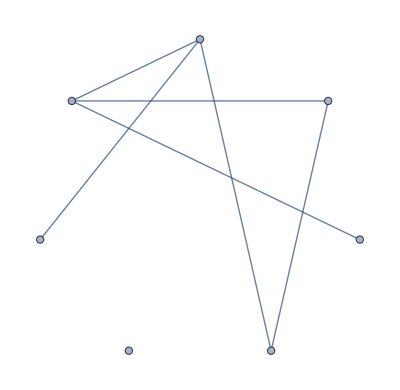

```mathematica
GraphComplement[grofs[[5]]]
```

```mathematica
ConnectedComponents[GraphComplement[grofs[[5]]]]
```

{{1,5,6,4,7,2},{3}}

```mathematica
MinimalPolynomial
```

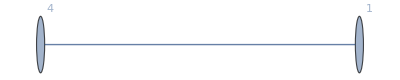
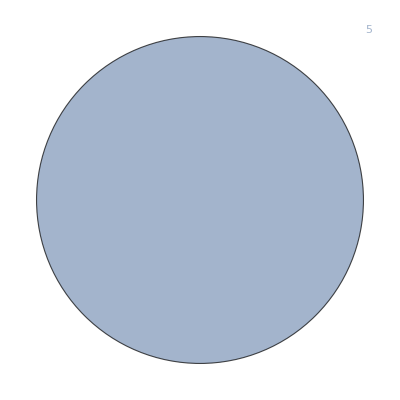
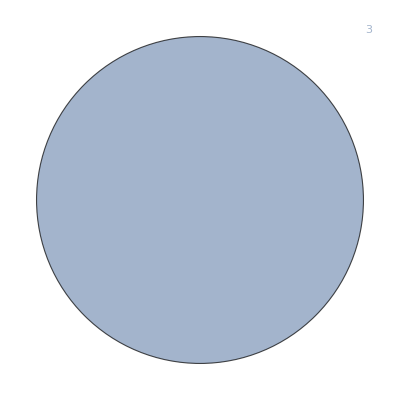
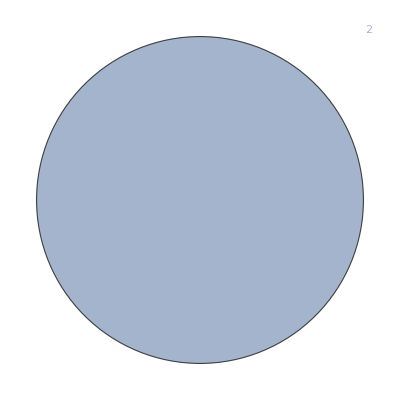
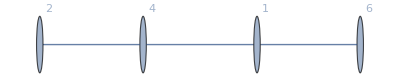
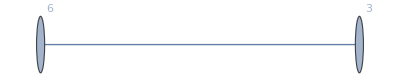
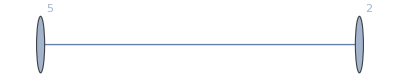
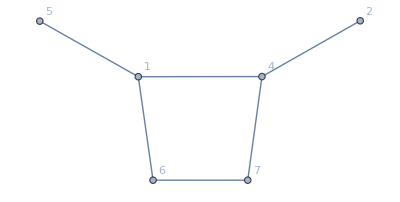
{n
5
remove
1→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},n
6
remove
3→{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},n
7
remove
6→{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},n
8
remove
10→{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},n
9
remove
15→{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Table[Column[{"n",Style[count,Red],"remove",(count-3)(count-4)/2}]->Map[
With[{g=GraphComplement[First[#]]},Framed[
Table[

With[
{h=Subgraph[g,c]},
Graph[VertexList[h],EdgeList[h],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]

,
{c,ConnectedComponents[g]}
]
]
]
&,Tally[Select[grofs,VertexCount[#]==count&],IsomorphicGraphQ]
],{count,5,9}]
```